```mathematica
SetDirectory["C:\\Users\\artsa\\Downloads\\datos_abiertos_covid19 - 1"]
```

C:\Users\artsa\Downloads\datos_abiertos_covid19 - 1

```mathematica
data=Import["200507COVID19MEXICO - copia.csv"]
```

{{FECHA_ACTUALIZACION,ID_REGISTRO,ORIGEN,SECTOR,ENTIDAD_UM,SEXO,ENTIDAD_NAC,ENTIDAD_RES,MUNICIPIO_RES,TIPO_PACIENTE,FECHA_INGRESO,FECHA_SINTOMAS,FECHA_DEF,INTUBADO,NEUMONIA,EDAD,NACIONALIDAD,EMBARAZO,HABLA_LENGUA_INDIG,DIABETES,EPOC,ASMA,INMUSUPR,HIPERTENSION,OTRA_COM,CARDIOVASCULAR,OBESIDAD,RENAL_CRONICA,TABAQUISMO,OTRO_CASO,RESULTADO,MIGRANTE,PAIS_NACIONALIDAD,PAIS_ORIGEN,UCI},{2020-05-07,181b6b,1,4,5,2,5,5,35,1,2020-01-28,2020-01-28,9999-99-99,97,2,26,1,97,2,2,2,2,2,2,2,2,2,2,1,99,1,99,MÃ©xico,99,97},117208,{2020-05-07,0bc665,2,12,9,2,15,9,5,1,2020-05-07,2020-05-06,9999-99-99,97,2,23,1,97,2,2,2,2,2,2,2,2,2,2,2,1,3,99,MÃ©xico,99,97},{2020-05-07,1a5ec1,1,12,9,1,9,15,31,1,2020-05-07,2020-05-03,9999-99-99,97,2,46,1,2,2,2,2,2,2,2,2,2,2,2,2,2,3,99,MÃ©xico,99,97}}
 |  |  |  |

```mathematica
length=Length[data]
```

117212

```mathematica
data[[1,13]]
```

FECHA_DEF

```mathematica
def=Table[data[[i,13]],{i,2,length}]
```

{9999-99-99,2020-03-28,9999-99-99,9999-99-99,9999-99-99,9999-99-99,9999-99-99,9999-99-99,9999-99-99,9999-99-99,9999-99-99,9999-99-99,9999-99-99,9999-99-99,9999-99-99,9999-99-99,9999-99-99,9999-99-99,9999-99-99,9999-99-99,9999-99-99,9999-99-99,9999-99-99,2020-04-02,9999-99-99,9999-99-99,9999-99-99,9999-99-99,117155,9999-99-99,9999-99-99,9999-99-99,9999-99-99,9999-99-99,9999-99-99,9999-99-99,9999-99-99,9999-99-99,9999-99-99,9999-99-99,9999-99-99,9999-99-99,9999-99-99,9999-99-99,9999-99-99,9999-99-99,9999-99-99,9999-99-99,9999-99-99,9999-99-99,9999-99-99,9999-99-99,9999-99-99,9999-99-99,9999-99-99,9999-99-99,9999-99-99}
 |  |  |  |

```mathematica
DateString[def[[1]]]
```

9999-99-99

```mathematica
Table[DateList[{DateString[def[[i]]],{"Year","-","Month","-","Day"}}], {i,1,length-1}]
```

{{10007,6,7,0,0,0.},{2020,3,28,0,0,0.},{10007,6,7,0,0,0.},{10007,6,7,0,0,0.},{10007,6,7,0,0,0.},{10007,6,7,0,0,0.},{10007,6,7,0,0,0.},{10007,6,7,0,0,0.},{10007,6,7,0,0,0.},{10007,6,7,0,0,0.},{10007,6,7,0,0,0.},{10007,6,7,0,0,0.},117187,{10007,6,7,0,0,0.},{10007,6,7,0,0,0.},{10007,6,7,0,0,0.},{10007,6,7,0,0,0.},{10007,6,7,0,0,0.},{10007,6,7,0,0,0.},{10007,6,7,0,0,0.},{10007,6,7,0,0,0.},{10007,6,7,0,0,0.},{10007,6,7,0,0,0.},{10007,6,7,0,0,0.},{10007,6,7,0,0,0.}}
 |  |  |  |

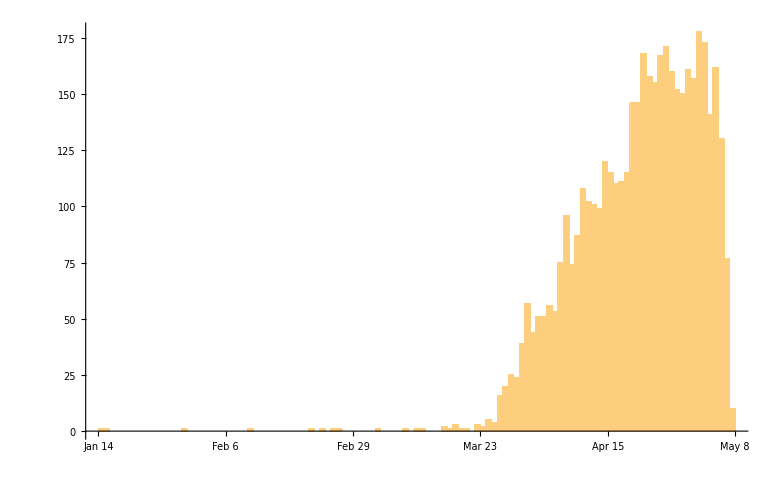

```mathematica
Timing[DateHistogram[def, "Day"]]
```